## Definiciones

```mathematica
SetDirectory[NotebookDirectory[]];Get["QuantumWalks.wl"]
```

```mathematica
(*moneda*)
ClearAll[c]
c[θ_,α_,ϕ_]:=FullSimplify[MatrixExp[-I*θ/2.*({Sin[α]Cos[ϕ],Sin[α]Sin[ϕ],Cos[α]}.(PauliMatrix/@{1,2,3}))]]
```

```mathematica
(*shift*)
ClearAll[S]
S[t_]:=KroneckerProduct[DiagonalMatrix[ConstantArray[1,2t],1],{{0,0},{0,1.}}]+KroneckerProduct[DiagonalMatrix[ConstantArray[1,2t],-1],{{1.,0},{0,0}}]
```

```mathematica
S[1].{0,0,1,0,0,0}
```

{0.,0.,0.,0.,1.,0.}

```mathematica
(*paso DTQW*)
ClearAll[U]
U[t_,θ_,α_,ϕ_]:=S[t].KroneckerProduct[IdentityMatrix[2t+1],c[θ,α,ϕ]]
```

```mathematica
U[1,θ,α,ϕ]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Sin[α] Sin[θ/2] (-ⅈ Cos[ϕ]+Sin[ϕ]) | Cos[θ/2]+ⅈ Cos[α] Sin[θ/2] | 0 | 0
Cos[θ/2]-ⅈ Cos[α] Sin[θ/2] | Sin[α] Sin[θ/2] (-ⅈ Cos[ϕ]-Sin[ϕ]) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Sin[α] Sin[θ/2] (-ⅈ Cos[ϕ]+Sin[ϕ]) | Cos[θ/2]+ⅈ Cos[α] Sin[θ/2]
0 | 0 | Cos[θ/2]-ⅈ Cos[α] Sin[θ/2] | Sin[α] Sin[θ/2] (-ⅈ Cos[ϕ]-Sin[ϕ]) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
U[2,θ,α,ϕ].ArrayPad[U[1,θ,α,ϕ].{0,0,1,0,0,0},2]/.{θ->0.52Pi,α->0.23Pi,ϕ->1.75Pi}
```

{0,-0.0469526-0.419743 ⅈ,0,0,-0.232397+0. ⅈ,-0.419743-0.0469526 ⅈ,0,0,0.169606-0.748631 ⅈ,0}

```mathematica
(*DTQWAnalytical*)
ClearAll[DTQWAnalytical]
DTQWAnalytical[t_,θ_,α_,ϕ_]:=Fold[ArrayPad[U[#2,θ,α,ϕ].#1,2]&,{0,0,0,1,0,0},Range[t]]
DTQWAnalyticalAnalytical[psi0_,t_,theta_,alpha_,phi_]:=Module[{validInput},validInput=MatchQ[psi0,{_?NumericQ,_?NumericQ,_?NumericQ,_?NumericQ,_?NumericQ,_?NumericQ}];
If[!validInput,Message[DTQWAnalyticalAnalytical::invalidpsi0,psi0];
Return[$Failed];];
Fold[ArrayPad[U[#2,theta,alpha,phi].#1,2]&,psi0,Range[t]]]

DTQWAnalyticalAnalytical::invalidpsi0="ψ0 debe ser una lista de 6 elementos numéricos. Se recibió: `1`.";
```

```mathematica
(*probabilidades espacio*)
ProbDistPosition[ψ_]:=Total/@(Abs[Partition[ψ,2]]^2)
```

```mathematica
ProbDistPosition[DTQWAnalyticalAnalytical[{0,0,1,0,0,0},3,θ,α,ϕ]]/.{θ->0.52Pi,α->0.23Pi,ϕ->1.75Pi}
```

{0,0.136932,0.,0.108026,0.,0.302759,0.,0.452283,0}

```mathematica
(*expected position*)
ClearAll[ExpPosition]
ExpPosition[t_,θ_,α_,ϕ_]:=ProbDistPosition[DTQWAnalyticalAnalytical[t,θ,α,ϕ]].Range[-t-1,t+1]
ExpPosition[ψ_]:=Module[{t=(Length[ψ]/2-3)/2},Chop[ProbDistPosition[ψ].Range[-t-1,t+1]]]
```

```mathematica
MyManipulate[t_]:=
Manipulate[
Plot[ExpPosition[t],{θ,0,2Pi},
PlotRange->{All,{-(t+0.05t),t+0.05t}},
Frame->True,
FrameLabel->{HoldForm[θ], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->30],
ImageSize->600,
PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = |1⟩, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π",Black,FontSize->25],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}}
]
,{α,0,Pi},{ϕ,0,2Pi}]
```

## Cálculos

```mathematica
t=5;
Manipulate[
Plot[Evaluate[ExpPosition[#,θ,α,ϕ]&/@Range[t]],{θ,0,2Pi},
PlotRange->{All,{-(t+0.05t),t+0.05t}},
Frame->True,
FrameLabel->{HoldForm[θ], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->1000,
PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = |1⟩, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π",Black,FontSize->28],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}}
]
,{α,0,Pi},{ϕ,0,2Pi}]
```

```mathematica
Export["/home/jadeleon/Documents/quantum_walks/ja/video.mp4",frames,"ImageSize"->480,"FrameRate"->16]
```

/home/jadeleon/Documents/quantum_walks/ja/video.mp4

```mathematica
t=5;
Manipulate[
Plot[Evaluate[ExpPosition[DTQWAnalyticalAnalytical[{0,0,1.,0,0,0},#,θ,α,ϕ]]&/@Range[5]],{θ,0,2Pi},
PlotRange->{All,{-(t+0.05t),t+0.05t}},
Frame->True,
FrameLabel->{HoldForm[θ], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->1000,
PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = |0⟩, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π",Black,FontSize->28],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}}
]
,{α,0,Pi},{ϕ,0,2Pi}]
```

```mathematica
t=5;
Manipulate[
Plot[Evaluate[ExpPosition[DTQWAnalyticalAnalytical[{0,0,1./√2.,1./√2.,0,0},#,θ,α,ϕ]]&/@Range[5]],{θ,0,2Pi},
PlotRange->{All,{-(t+0.05t),t+0.05t}},
Frame->True,
FrameLabel->{HoldForm[θ], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->600,
PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = |0⟩, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π",Black,FontSize->28],
PlotLegends->Range[5],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}}
]
,{α,0,Pi},{ϕ,0,2Pi}]
```

```mathematica
ψ=DTQW[ψ0,t,coinOperator];
ClearAll[ExpValPosition]
ExpValPosition[ψ_,t_]:=PositionProbabilityDistribution[ψ,t].Range[-t-1,t+1]
```

```mathematica
PositionProbabilityDistribution[DTQW[ψ0,2,coinOperator],2]
```

{0,0.543026,0,0.442628,0,0.014346,0}

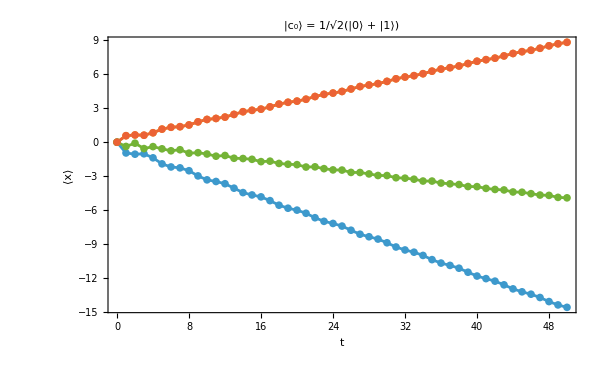

```mathematica
ψ0={1,1}/√2.;tmax=50;
coinOperator=c[3Pi/2.,0.39Pi,1.3Pi];
ListPlot[{Prepend[Table[{t,ExpValPosition[DTQW[ψ0,t,coinOperator],t]},{t,tmax}],{0,0}],Prepend[Table[{t,ExpValPosition[DTQW[ψ0,t,-c[Pi/2.,0.39Pi,1.3Pi]],t]},{t,tmax}],{0,0}],Prepend[Table[{t,ExpValPosition[DTQW[ψ0,t,c[Pi,0.39Pi,1.3Pi]],t]},{t,tmax}],{0,0}],Prepend[Table[{t,ExpValPosition[DTQW[ψ0,t,c[Pi,0.39Pi,1.3Pi].c[3Pi/2,0.39Pi,1.3Pi]],t]},{t,tmax}],{0,0}]},
Joined->True,
Mesh->All,
Frame->True,
FrameLabel->{TraditionalForm@HoldForm[t], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->600,
PlotLabel->Style["|c_0⟩ = 1/√2(|0⟩ + |1⟩)",Black,FontSize->28]
]
```

```mathematica
c[Pi,0.39Pi,1.3Pi].c[3Pi/2.,0.39Pi,1.3Pi]//Chop//MatrixForm
```

(-0.707107+0.239524 ⅈ | -0.538242-0.391055 ⅈ
0.538242-0.391055 ⅈ | -0.707107-0.239524 ⅈ)

```mathematica
-c[Pi/2.,0.39Pi,1.3Pi]//Chop//MatrixForm
```

(-0.707107+0.239524 ⅈ | -0.538242-0.391055 ⅈ
0.538242-0.391055 ⅈ | -0.707107-0.239524 ⅈ)

```mathematica
c[θ,α,ϕ]//Chop//MatrixForm
```

(1. Cos[0.5 θ]-(0.+1. ⅈ) Cos[α] Sin[0.5 θ] | (0.-1. ⅈ) ⅇ^(-ⅈ ϕ) Sin[α] Sin[0.5 θ]
Sin[α] Sin[0.5 θ] ((0.-1. ⅈ) Cos[ϕ]+1. Sin[ϕ]) | 1. Cos[0.5 θ]+(0.+1. ⅈ) Cos[α] Sin[0.5 θ])